```mathematica
ClearAll;
```

```mathematica
<<IGraphM``
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

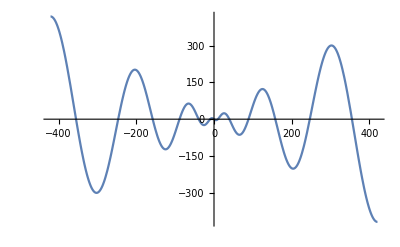

-Graphics3D-

```mathematica
(*Schwefel' s Function*)
fun4Name="Schwefel' s Function";
fun4[x_]:=Module[{l=Length@x}, Sum[-x[[i]] Sin[Sqrt[Abs[x[[i]]]]], {i,l}]];
Plot[fun4@{x},{x,-420.969,420.969}]
Plot3D[fun4@{x1,x2},{x1,-420.969,420.969},{x2,-420.969,420.969}]
```

```mathematica
draw[matrix_]:=Module[{f,g,adjacencyMatrix,vertices},
adjacencyMatrix=matrix;
adjacencyMatrix=Rescale@adjacencyMatrix/. 0->∞//N;
f[pts_List,e_]:=Block[
{s=0.015,weight=PropertyValue[{g,e},EdgeWeight]},
{
ColorData["TemperatureMap"][weight],
Arrowheads[{{s,0.1},{s,0.9}}],
AbsoluteThickness[weight*15],
Arrow[pts]
}
];

vertices=Join[{{0,0}},Table[{4 Cos[a],4 Sin[a]},{a,Pi/4,2 Pi,Pi/4}],Table[{7 Cos[a],7 Sin[a]},{a,0,5 Pi/3,Pi/6}]][[1;;Length@adjacencyMatrix]];
g=WeightedAdjacencyGraph[adjacencyMatrix,
VertexLabels->"Name",
EdgeLabels->(*"EdgeWeight"*)None,
EdgeShapeFunction->f,
VertexLabelStyle->Directive[Black,Bold,20],
ImageSize->Large,
Background->GrayLevel@0.8,
VertexCoordinates->vertices
(*,
VertexCoordinates->vertices*)
];
Return@g;
];
```

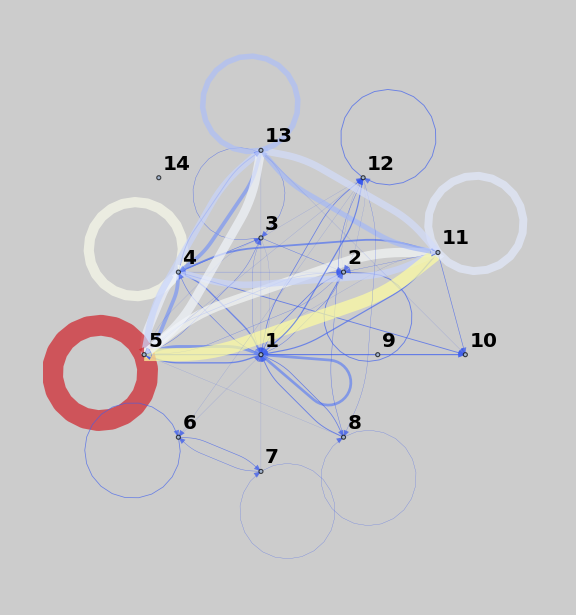

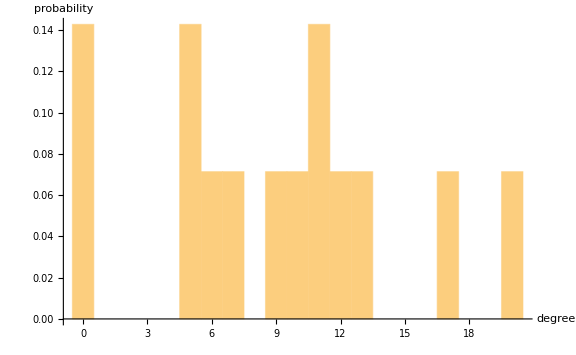

```mathematica
realData={
	{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} };
realData=realData[[All,1;;Length@realData]];
g1=draw@realData
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
pts[m_,r_]:=Module[{pts,DCr, DCm, CCr,CCm,BCm, BCr, EVCr, EVCm, ICr, ICm},
pts=0;

DCm = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@m];
DCr = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@r];

CCm=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@m];
CCr=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@r];

BCm=Mean[IGBetweenness@IGWeightedAdjacencyGraph@m];
BCr=Mean[IGBetweenness@IGWeightedAdjacencyGraph@r];

EVCm=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@m];
EVCr=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@r];
(*Information centrality*)
pts=((DCr-DCm)/DCr)^2+((CCr-CCm)/CCr)^2+((BCr-BCm)/BCr)^2+((EVCr-EVCm)/EVCr)^2;
pts*=1000;
Return@pts
];
```

gBestPositionIndex initial = 9

gBestPosition before loop = {-2.86985,3.93541,4.19978,-1.65497,3.19482}

swarmPosition before loop = {{0.293422,-0.736621,1.08399,3.08352,1.51827},{-0.266181,4.10013,-4.07252,4.23932,-3.25778},{-3.69793,0.408369,-3.76792,-4.96683,3.49532},{-4.62583,0.64976,-0.334503,-1.34786,-4.84964},{3.5707,3.97418,-4.72002,-4.40866,-1.21175},{-2.56437,-4.79451,-4.10136,-3.87376,-3.28436},{-2.96852,-0.0782281,3.30802,-3.75311,3.07969},{-0.535645,2.73881,-0.239067,0.487227,-4.20641},{-2.86985,3.93541,4.19978,-1.65497,3.19482},{1.22628,1.14256,-3.3404,-0.0933195,0.640678},{0.436003,4.97972,-4.50003,-2.83714,-4.11875},{1.31774,-1.49761,-2.85956,1.73561,0.00233274},{3.96578,4.18061,-0.841222,-3.84402,-0.305133},{-4.69518,-1.46752,-0.632768,-4.93706,1.58946}}

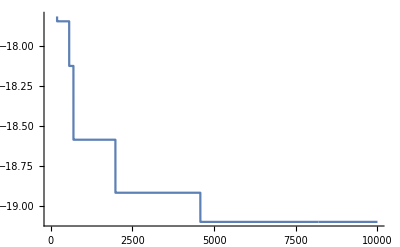

```mathematica
Clear[adjCitationData];
Clear[inertia];
Clear[swarmPosition];
Clear[swarmVelocity];
Clear[pBestPosition];
Clear[pBestCost];
Clear[swarmPositionCostTemp];
Clear[swarmPositionTemp];
Clear[swarmPositionCost];
Clear[gBestPosition];
Clear[gBestCost];
Clear[boundry];
Clear[historyGBestCost];
Clear[historyGBestPosition];

Clear[f];
Clear[fLowerBound];
Clear[fUpperBound];
Clear[swarmDim];
Clear[NP];
Clear[c1];
Clear[c2];
Clear[w];
Clear[iterations];

PSOAlgorithm[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_
]:=Module[
{
inertia,swarmPosition,swarmPositionTemp,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,swarmPositionCostTemp,gBestPosition,gBestPositionIndex,
gBestCost,FitnessFunction,fLowerBound,fUpperBound,f1,
rand1,
rand2,
i,j,k,n,l,
boundry,
historyGBestPosition,historyGBestCost,communicationList,
it
},

inertia=ConstantArray[0,{NP,swarmDim}];
swarmPosition=ConstantArray[0,{NP,swarmDim}];
swarmPositionTemp={};
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=ConstantArray[0,{NP,swarmDim}];
pBestCost=Table[0,NP];
swarmPositionCostTemp=Table[0,swarmDim];
swarmPositionCost=Table[0,NP];
swarmPositionCostTemp=0;
gBestPosition=Table[0,swarmDim];
gBestCost=0;
gBestPositionIndex;
FitnessFunction=f;
f1=FitnessFunction;
fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];
boundry={};
historyGBestPosition={};
historyGBestCost={};
communicationList={};

(*Initialization start*)
swarmPosition=RandomReal[{fLowerBound,fUpperBound},{NP,swarmDim}];
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=swarmPosition;
f1[x__]:=Re[Map[FitnessFunction,{x}]];

swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];
gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
gBestPositionIndex=First@First@Position[swarmPositionCost,gBestCost];
Print["gBestPositionIndex initial = ", gBestPositionIndex];
Print["gBestPosition before loop = " ,gBestPosition];
Print["swarmPosition before loop = " ,swarmPosition];

(*Main Loop*)

it=0;
While[it< iterations,
{

(*Update the velocity and position vectors*)
For[i=1,i≤  (NP),i++,
For[j=1,j≤  (swarmDim),j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
For[j=1,j<=swarmDim,j++,
If[swarmPosition[[i,j]]<fLowerBound,swarmPosition[[i,j]]=RandomReal@fLimit];
If[swarmPosition[[i,j]]>fUpperBound,swarmPosition[[i,j]]=RandomReal@fLimit];
];
n=0;
f1[x__]:=Map[FitnessFunction,{x}];
swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];
If[pBestCost[[i]]<= gBestCost,
{
(*Print@"----Particle updating the gBest-------";*)
(*Capture here*)
(*Here link is created in two cases: 
	1. When particle replaces the gBest, a link is created between particle at current position and the particle at gBest position.
	2. A link is also created between the particle at current position and all the other particles in the swarm. 
*)
AppendTo[communicationList,First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex]; 
For[l=1,l<=Length@swarmPosition,l++,
If[l== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, i <-> l];
];
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];
gBestPositionIndex=First@First@Position[swarmPosition, pBestPosition[[i]] ];
};
];
}
];
];
AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];
,it++
}];
Return@{swarmPosition, pBestPosition,pBestCost,gBestPosition,gBestCost ,historyGBestPosition, historyGBestCost, communicationList,
swarmPositionCost};
];
(*PSOAlgorithm[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_]*)
(*outputFromPso=PSOAlgorithm[fun4,{-5,5} ,3,14,1.49445,1.49445,0.729,40000];*)

outputFromPso=PSOAlgorithm[fun4,{-5,5} ,5,14,1.49445,1.49445,0.729,10000];
ListPlot[outputFromPso[[7]],Joined->True]

(*outputFromPso=PSOAlgorithm[fun3,{-5,5} ,3,14,-420.969,420.969,0.729,100];
ListPlot[outputFromPso[[7]],Joined->True]*)
```

```mathematica
capturedDataFromPSO=outputFromPso[[8]];
capturedDataFromPSO
```

{2<->9,2<->1,2<->2,2<->3,2<->4,2<->5,2<->6,2<->7,2<->8,2<->10,2<->11,2<->12,2<->13,2<->14,4<->2,4<->1,4<->3,4<->4,4<->5,4<->6,4<->7,4<->8,4<->9,4<->10,4<->11,4<->12,4<->13,4<->14,3<->4,3<->1,3<->2,3<->3,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,3<->13,3<->14,12<->3,12<->1,12<->2,12<->4,12<->5,12<->6,12<->7,12<->8,12<->9,12<->10,12<->11,12<->12,12<->13,12<->14,11<->12,11<->1,11<->2,11<->3,11<->4,11<->5,11<->6,11<->7,11<->8,11<->9,11<->10,11<->11,11<->13,11<->14,3<->11,3<->1,3<->2,3<->3,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,3<->12,3<->13,3<->14,12<->3,12<->1,12<->2,12<->4,12<->5,12<->6,12<->7,12<->8,12<->9,12<->10,12<->11,12<->12,12<->13,12<->14,5<->12,5<->1,5<->2,5<->3,5<->4,5<->5,5<->6,5<->7,5<->8,5<->9,5<->10,5<->11,5<->13,5<->14}

```mathematica
(*Sorting the captured data in ascending order for nodes*)
sortedCapturedDataFromPSO = Sort[capturedDataFromPSO,#1[[1]]<#2[[1]]&]
```

{2<->14,2<->13,2<->12,2<->11,2<->10,2<->8,2<->7,2<->6,2<->5,2<->4,2<->3,2<->2,2<->1,2<->9,3<->14,3<->13,3<->12,3<->10,3<->9,3<->8,3<->7,3<->6,3<->5,3<->4,3<->3,3<->2,3<->1,3<->11,3<->14,3<->13,3<->12,3<->11,3<->10,3<->9,3<->8,3<->7,3<->6,3<->5,3<->3,3<->2,3<->1,3<->4,4<->14,4<->13,4<->12,4<->11,4<->10,4<->9,4<->8,4<->7,4<->6,4<->5,4<->4,4<->3,4<->1,4<->2,5<->14,5<->13,5<->11,5<->10,5<->9,5<->8,5<->7,5<->6,5<->5,5<->4,5<->3,5<->2,5<->1,5<->12,11<->14,11<->13,11<->11,11<->10,11<->9,11<->8,11<->7,11<->6,11<->5,11<->4,11<->3,11<->2,11<->1,11<->12,12<->14,12<->13,12<->12,12<->11,12<->10,12<->9,12<->8,12<->7,12<->6,12<->5,12<->4,12<->2,12<->1,12<->3,12<->14,12<->13,12<->12,12<->11,12<->10,12<->9,12<->8,12<->7,12<->6,12<->5,12<->4,12<->2,12<->1,12<->3}

```mathematica
(*Creating adjacency matrix form for the captured data*)
matrixFormSortedCapturedDataFromPSO = AdjacencyMatrix@capturedDataFromPSO //MatrixForm
```

(1 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 4 | 2 | 2
2 | 1 | 1 | 3 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1
2 | 1 | 1 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
2 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 3 | 1 | 1
3 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0)

```mathematica
testList=AdjacencyMatrix@sortedCapturedDataFromPSO;
```

```mathematica
(*Creating separate list for all the data captured*)
capturedFromPSO={};
For[i=1,i<=Length@testList,i++,

subList={};
For[j=1,j<=Length@testList,j++,
AppendTo[subList, testList[[i]][[j]]];
];
AppendTo[capturedFromPSO, subList];
];
```

```mathematica
capturedFromPSO
```

{{1,1,1,3,2,1,1,1,1,2,2,3,1,1},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{3,2,2,2,3,2,2,2,2,3,3,4,2,2},{2,1,1,3,1,1,1,1,1,2,2,3,1,1},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{2,1,1,3,2,1,1,1,1,1,2,3,1,1},{2,1,1,3,2,1,1,1,1,2,1,3,1,1},{3,2,2,4,3,2,2,2,2,3,3,2,2,2},{1,0,0,2,1,0,0,0,0,1,1,2,0,0},{1,0,0,2,1,0,0,0,0,1,1,2,0,0}}

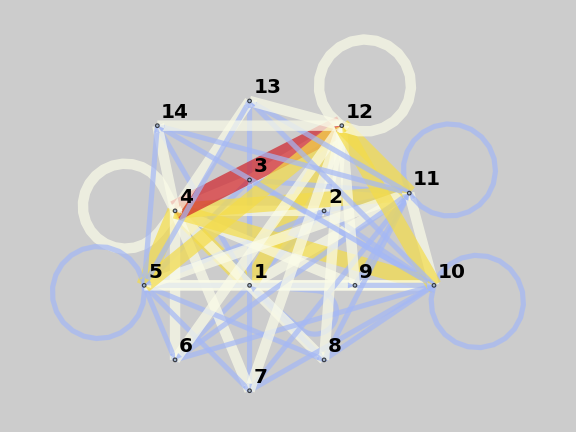

{15,6,6,15,15,6,6,6,6,15,15,15,6,6}

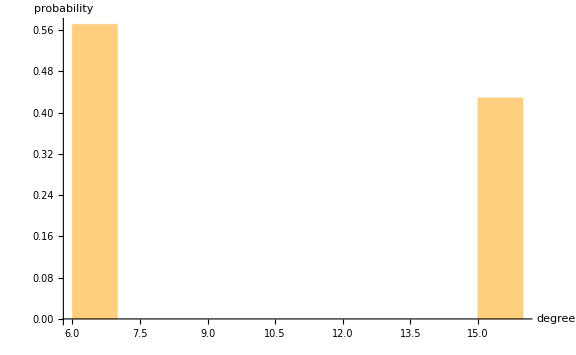

```mathematica
capturedFromPSO=capturedFromPSO[[All,1;;Length@capturedFromPSO]];
g1=draw@capturedFromPSO
VertexDegree[g1]
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
pts[capturedFromPSO,realData]
```

7985.55